```mathematica
SetDirectory[NotebookDirectory[]];
```

## Vertical line

```mathematica
mub1={54.,56.};
Tc1={131.85747300,131.83529620};
p1=Transpose[{mub1,Tc1}];
mub2={104.,106.};
Tc2={131.05868700,131.01608120};
p2=Transpose[{mub2,Tc2}];
mub3={204.,206.};
Tc3={127.89577350,127.81047480};
p3=Transpose[{mub3,Tc3}];
mub4={304.,306.};
Tc4={122.49720000,122.36457190};
p4=Transpose[{mub4,Tc4}];
mub5={404.,406.};
Tc5={114.54239950,114.3538043};
p5=Transpose[{mub5,Tc5}];
mub6={604.,606.};
Tc6={87.877018,87.503298};
p6=Transpose[{mub6,Tc6}];
mub7={699.5,700.5};
Tc7={64.994636,64.65758};
p7=Transpose[{mub7,Tc7}];
```

```mathematica
Fit1=FindFit[p1,a x+b,{a,b},x];
Fit2=FindFit[p2,a x+b,{a,b},x];
Fit3=FindFit[p3,a x+b,{a,b},x];
Fit4=FindFit[p4,a x+b,{a,b},x];
Fit5=FindFit[p5,a x+b,{a,b},x];
Fit6=FindFit[p6,a x+b,{a,b},x];
Fit7=FindFit[p7,a x+b,{a,b},x];
Fit1p=FindFit[{PerpendicularBisector[p1][[1]],PerpendicularBisector[p1][[1]]-PerpendicularBisector[p1][[2]]},a x+b,{a,b},x];
Fit2p=FindFit[{PerpendicularBisector[p2][[1]],PerpendicularBisector[p2][[1]]-PerpendicularBisector[p2][[2]]},a x+b,{a,b},x];
Fit3p=FindFit[{PerpendicularBisector[p3][[1]],PerpendicularBisector[p3][[1]]-PerpendicularBisector[p3][[2]]},a x+b,{a,b},x];
Fit4p=FindFit[{PerpendicularBisector[p4][[1]],PerpendicularBisector[p4][[1]]-PerpendicularBisector[p4][[2]]},a x+b,{a,b},x];
Fit5p=FindFit[{PerpendicularBisector[p5][[1]],PerpendicularBisector[p5][[1]]-PerpendicularBisector[p5][[2]]},a x+b,{a,b},x];
Fit6p=FindFit[{PerpendicularBisector[p6][[1]],PerpendicularBisector[p6][[1]]-PerpendicularBisector[p6][[2]]},a x+b,{a,b},x];
Fit7p=FindFit[{PerpendicularBisector[p7][[1]],PerpendicularBisector[p7][[1]]-PerpendicularBisector[p7][[2]]},a x+b,{a,b},x];
```

```mathematica
funcmu=Solve[r==√(((a mu+b-Tc)/Tc)^2+((mu-muc)/muc)^2)&&Im[r]==0,mu,Assumptions->{a>0,b<0,Tc>0,muc>0,mu<muc,a mu+b-Tc<0}]
```

{{mu→ConditionalExpression[(-a b muc^2+a muc^2 Tc+muc Tc^2)/(a^2 muc^2+Tc^2)-(√(-b^2 muc^2 Tc^2-2 a b muc^3 Tc^2-a^2 muc^4 Tc^2+a^2 muc^4 r^2 Tc^2+2 b muc^2 Tc^3+2 a muc^3 Tc^3-muc^2 Tc^4+muc^2 r^2 Tc^4))/(a^2 muc^2+Tc^2), ]}}

```mathematica
fmu[a_,b_,Tc_,muc_,r_]:=(-a b muc^2+a muc^2 Tc+muc Tc^2)/(a^2 muc^2+Tc^2)-1/(a^2 muc^2+Tc^2)(√(-b^2 muc^2 Tc^2-2 a b muc^3 Tc^2-a^2 muc^4 Tc^2+a^2 muc^4 r^2 Tc^2+2 b muc^2 Tc^3+2 a muc^3 Tc^3-muc^2 Tc^4+muc^2 r^2 Tc^4))
```

```mathematica
ft[a_,b_,Tc_,muc_,r_]:=a fmu[a,b,Tc,muc,r]+b
```

```mathematica
(*Export["direction.txt",FortranForm[(-a b muc^2+a muc^2 Tc+muc Tc^2)/(a^2 muc^2+Tc^2)-1/(a^2 muc^2+Tc^2)(√(-b^2 muc^2 Tc^2-2 a b muc^3 Tc^2-a^2 muc^4 Tc^2+a^2 muc^4 r^2 Tc^2+2 b muc^2 Tc^3+2 a muc^3 Tc^3-muc^2 Tc^4+muc^2 r^2 Tc^4))]];*)
```

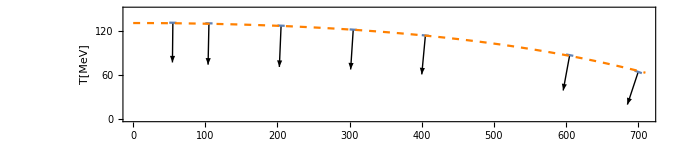

```mathematica
phase=Show[Graphics[{Arrowheads[{-0.03,0}],
Arrow[{{54.4,a x+b/.Fit1p/.x->54.4},{55,a x+b/.Fit1p/.x->55}}],Arrow[{{103.8,a x+b/.Fit2p/.x->103.8},{105,a x+b/.Fit2p/.x->105}}],Arrow[{{202.6,a x+b/.Fit3p/.x->202.6},{205,a x+b/.Fit3p/.x->205}}],Arrow[{{301.4,a x+b/.Fit4p/.x->301.4},{305,a x+b/.Fit4p/.x->305}}],Arrow[{{400.,a x+b/.Fit5p/.x->400},{405,a x+b/.Fit5p/.x->405}}],Arrow[{{596.,a x+b/.Fit6p/.x->596},{605,a x+b/.Fit6p/.x->605}}],Arrow[{{685.,a x+b/.Fit7p/.x->685},{700,a x+b/.Fit7p/.x->700}}]}],Plot[{a x+b/.Fit1},{x,50,60}],Plot[{a x+b/.Fit2},{x,100,110}],Plot[a x+b/.Fit3,{x,200,210}],Plot[a x+b/.Fit4,{x,300,310}],Plot[a x+b/.Fit5,{x,400,410}],Plot[a x+b/.Fit6,{x,600,610}],Plot[a x+b/.Fit7,{x,695,705}],Plot[a+b x^2+c x^4/.{a->131.41089150780581,b->-0.00009005991176280982,c->-8.785096239693687*^-11},{x,0,710},PlotStyle->{Orange,Dashed}],PlotRange->{{0,710},{0,150}},AspectRatio->150/710,Frame->True,FrameLabel->{"μ_B[MeV]","T[MeV]"}]
```

```mathematica
Export["phase.pdf",phase]
```

phase.pdf